# Midterm 2

Note: If you get to a part where you know exactly what you need to do but don’t know how to make Mathematica do it, please write clearly and explicitly what you would do. We will give you at least partial credit for correct reasoning even if the code doesn’t quite work. (But do your best to get the code to work! All Mathematica techniques you will need for this exam you have already seen in some form in the homework.)

## Problem 4

A hoop of mass M and radius R is free to roll without slipping on a horizontal surface. A particle of mass m is placed inside the hoop and can slide along the inside of the hoop without friction. Plot the motion of the hoop and the particle if the particle is displaced by 45 degrees above the bottom of the hoop and the system is released from rest. From the plot, estimate the period of oscillation to the nearest tenth of a second.

-Graphics-

Use the following values (don’t plug them in until the end):
M: 0.5 kg
R: 0.25 m
m: 0.125 kg
g: 9.8 m/s^2 
Note that the moment of inertia for a hoop is MR^2.

```mathematica
Quit[]
```

```mathematica
Clear["'*"]
```

(10 points) Determine the Lagrangian for the system. (Hint: It may be helpful to consider the position (X, Y) of the center of the hoop and the position (x, y) of the particle, and then re-express these in terms of generalized coordinates of your choosing.)
NOTE: For these Mathematica problems, if you do some work on a separate piece of paper and want to submit it for possible partial credit, please append it to your written submissions and clearly indicate which problem your work corresponds to. If your work is not neat enough to be deciphered reasonably easily, it will be difficult for us to award partial credit.

```mathematica
(* Generalized coordinates x - horizontal distance of center of mass of hoop; theta - particle's displacement along hoop from bottom of hoop *)
T=1/2*R^2*thetadot^2*M*R^2+1/2*M*xdot^2+1/2*m*thetadot^2;
U=m*g*R*(1-Cos[theta]);
L=T-U
```

(m thetadot^2)/2+1/2 M R^4 thetadot^2+(M xdot^2)/2-g m R (1-Cos[theta])

(3 points) Set up the equations of motion. Don’t forget to include the explicit time dependence (here and further down, replace “var1” and “var2” with whatever variable names you have chosen).

```mathematica
rule={theta->theta[t],thetadot->theta'[t],x->x[t],xdot->x'[t]};
dLdtheta=D[L,theta]/.rule
dLdthetadot=D[L,thetadot]/.rule
dLdx=D[L,x]/.rule
dLdxdot=D[L,xdot]/.rule

eqtheta=dLdtheta==D[dLdthetadot,t];
eqx=dLdx==D[dLdxdot,t];
```

-g m R Sin[theta[t]]

m theta'[t]+M R^4 theta'[t]

0

M x'[t]

Solve the equations (don’t forget to plug in appropriate initial conditions) and plot the motion of the system (2 points). Estimate the period of oscillation to the nearest tenth of a second (2 points).

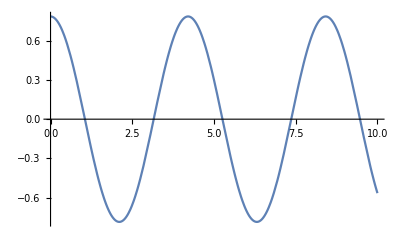

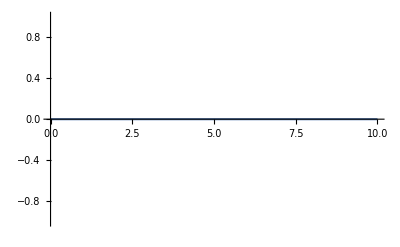

```mathematica
M=0.5;
R=0.25;
m=0.125;
g=9.8; 
sol1=NDSolve[{eqtheta,eqx,theta[0]==Pi/4,theta'[0]==0,x[0]==0,x'[0]==0},{theta,x},{t,0,10}];
Plot[theta[t]/.sol1,{t,0,10}]
Plot[x[t]/.sol1,{t,0,10}]
```

Period of oscillation: 
4.2 seconds 

(3 points) What physical quantity is conserved in this system?

The Lagrangian is independent of x. Therefore, x is an ignorable coordinate and its corresponding generalized momentum must be constant. This means that the momentum in the horizontal direction, or px, is conserved/constant. (Recall Fi  = d/dt pi. If Fi is zero, then the time derivative of the momentum must be constant).

## Problem 5

Two particles of mass m1 = 5 kg and m2 = 15 kg interact via a central force with a potential energy given by U = -gamma/r, with gamma = 2 × 10^5 J m. At time t = 0, particle 1 is at position r10 = (-75 m, -300 m, 0) and has velocity v10 = (6 m/s, 0.5 m/s, 0) as measured in the center of mass frame. No external forces are present.

```mathematica
Quit[]
Clear["`*"]
```

Determine the initial position r20 of particle 2 (1 point), initial velocity v20 of particle 2 (1 point), the magnitude of the total angular momentum Lmag of the system (1 point), and the total energy Etot of the system (1 point). Comment on the physical significance of the sign of the total energy (2 points).

```mathematica
m1=5.0;
m2=15.0;
r10={-75,-300,0};
v10={6,0.5,0};

gamma=2*10^5;

r20=-m1/m2*r10
v20=-m1/m2*v10

r0=r10-r20;
U0=-gamma/Norm[r0];

Lmag=Norm[Cross[r10,m1*v10]+Cross[r20,m2*v20]]
Etot=1/2*m1*Norm[v10]^2+1/2*m2*Norm[v20]^2+U0
```

{25.,100.,0.}

{-2.,-0.166667,0.}

11750.

-364.238

Physical significance of the sign of the total energy:

Calculate the reduced mass mu of the system (1 point). Write down the equations of motion for the separation distance r[t] and the angle phi[t] (2 points) Be sure to include the explicit time dependence, i.e. r[t] and phi[t].

```mathematica
M=m1+m2;
mu=m1*m2/M
req=mu*r''[t]==-gamma/r[t]^2+Lmag^2/(mu*r[t]^3)
phieq=phi'[t]==Lmag/(mu*r[t]^2)
```

3.75

3.75 r''[t]==(3.68167×10^7)/r[t]^3-200000/r[t]^2

phi'[t]==3133.33/r[t]^2

Determine the initial values r0 and phi0 based on the information about the initial positions provided above (4 points). You may take as given that r’(0) = -2.58705 m/s, since this quantity is just a little bit tricky to determine. Solve the differential equations for r and phi (3 points).

```mathematica
r0mag=Norm[r10-r20];
phi0=Lmag/(mu*r0mag^2);
rdot0=-2.58705;
sol1=NDSolve[{req,phieq,r[0]==r0mag,r'[0]==rdot0,phi[0]==phi0},{r,phi},{t,0,200}];
```

Plot r(t) and use the graph to estimate the minimum and maximum separation between the two particles to the nearest 10 meters (2 points).

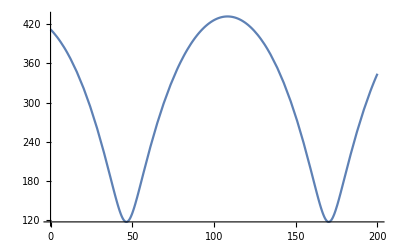

```mathematica
Plot[r[t]/.sol1,{t,0,200}]
```

Minimum separation: 120
Maximum separation: 435

Execute the code below to animate the trajectories of the two masses and explain why one of the masses has a smaller trajectory than the other (2 points). Note: The trajectories will not be neatly aligned with the x and y axes (unlike most of the examples shown in the book and homework).

```mathematica
Manipulate[ParametricPlot[{(m2/(m1+m2)){r[t]*Cos[phi[t]],r[t]*Sin[phi[t]]}/.sol1,(-m1/(m1+m2)){r[t]*Cos[phi[t]],r[t]*Sin[phi[t]]}/.sol1},{t,0,tf},PlotRange->{{-250,150},{-400,150}}],{tf,0.01,200}]
```

Explanation of why one of the masses has a smaller trajectory than the other:

The mass with the smaller trajectory is the bigger one, because it is closer to the center of mass of the system, so it does not have to move that much. 
Whereas the other mass can move really far away and not make as much of a difference because it is not as massive.